{conc[a,3],step[{a →^1 b }],step[{b →^1 c }],step[{c →^1 a }]}

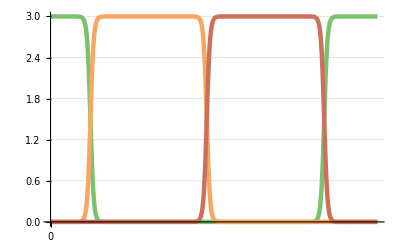

```mathematica
Get[NotebookDirectory[]<>"sequence.m"]
rsys=SequenceRsys[];
Print[rsys];
tmax=100;
sol=SimulateRxnsys[ExpandRsys[rsys], tmax];
PlotForPaper[Evaluate[{a[t],b[t],c[t]}/.sol], tmax, 200]
```